```mathematica
Clear["Global`*"];
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
ρ=N[1-1/10^9];
SIGMA=Table[ρ,10,10];
For[i=1,i≤10,i++,SIGMA[[i,i]]=1/ρ];
U[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_]=N[1/2 Simplify[{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}.LinearSolve[SIGMA,{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}]]];
dU[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_]=GradientG[U[x1,x2,x3,x4,x5,x6,x7,x8,x9,x10],{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}];
ddU[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_]=HessianH[U[x1,x2,x3,x4,x5,x6,x7,x8,x9,x10],{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}];
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{4.5×10^8,-5.×10^7,-5.×10^7,-5.×10^7,-5.×10^7,-5.×10^7,-5.×10^7,-5.×10^7,-5.×10^7,-5.×10^7},«8»,{-5.×10^7,-5.×10^7,«7»,4.5×10^8}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

501 3.9016×10^8 57.716 0.3 0.483046 3.92666×10^6 3.94087×10^8 3.9267×10^8 2.07965×10^-7 0.000611591 True {1,2,3,8,11} {1,11}

1002 37185.6 56.3132 0.630329 0.312374 374.893 37548.1 37560.5 7.28905×10^-8 0.000984973 False {1,2,3,11} {1,11}

1503 4150.33 49.3004 0.717648 0.218765 48.1485 4198.48 4118.21 1.17391×10^-7 0.00452593 True {1,3,4,10,11} {1,11}

2004 3751.12 74.0006 0.678199 0.453678 55.2824 4113.02 3806.4 1.71872×10^-7 0.00662641 False {1,4,6,7,11} {1,11}

2505 3967.8 44.1866 0.600362 0.357831 48.3466 4016.14 3746.66 1.42043×10^-7 0.00801795 True {1,6,7,11} {1,11}

3006 3423.79 28.419 0.551411 0.375479 51.6114 3612.59 3475.4 1.71872×10^-7 0.00602401 False {1,4,11} {1,11}

3507 3397.32 48.9085 0.74702 0.300645 50.8734 3448.19 3322.76 1.56247×10^-7 0.00662641 True {1,2,6,11} {1,11}

4008 3248.23 37.3081 0.523848 0.37085 52.0979 3301.45 3300.33 2.07965×10^-7 0.00547637 False {1,2,5,11} {1,11}

4509 3514.43 56.6918 0.846742 0.196905 46.6927 3561.12 3284.17 1.71872×10^-7 0.00662641 True {1,2,3,4,6,11} {1,11}

5010 3234.78 44.8345 0.664909 0.347402 49.3928 3644.23 3284.17 1.42043×10^-7 0.00662641 False {1,3,5,7,11} {1,11}

5511 3600.59 51.0141 0.704768 0.345199 43.6444 3644.23 3284.17 1.42043×10^-7 0.00662641 True {1,3,5,6,11} {1,11}

6012 3235.7 56.7353 0.773441 0.31206 48.4725 3644.23 3284.17 1.42043×10^-7 0.00662641 False {1,3,5,11} {1,11}

6513 3592.94 52.6738 0.642997 0.323724 51.2948 3644.23 3284.17 1.42043×10^-7 0.00662641 True {1,4,8,11} {1,11}

7014 3249.73 24.6984 0.39692 0.373648 34.4436 3644.23 3284.17 1.42043×10^-7 0.00662641 False {1,3,5,11} {1,11}

7515 3591.96 40.8622 0.580687 0.302072 52.2692 3644.23 3284.17 1.42043×10^-7 0.00662641 True {1,3,7,11} {1,11}

8016 3223.67 88.1254 0.512606 0.411419 60.5056 3644.23 3284.17 1.42043×10^-7 0.00662641 False {1,3,11} {1,11}

8517 3592.43 54.0952 0.743838 0.328421 51.8064 3644.23 3284.17 1.42043×10^-7 0.00662641 True {1,6,7,8,10,11} {1,11}

9018 3228.21 36.8637 0.579831 0.410028 55.9602 3644.23 3284.17 1.42043×10^-7 0.00662641 False {1,2,3,11} {1,3,11}

9519 3595.76 45.7844 0.390466 0.276381 48.4702 3644.23 3284.17 1.42043×10^-7 0.00662641 True {1,11} {1,11}

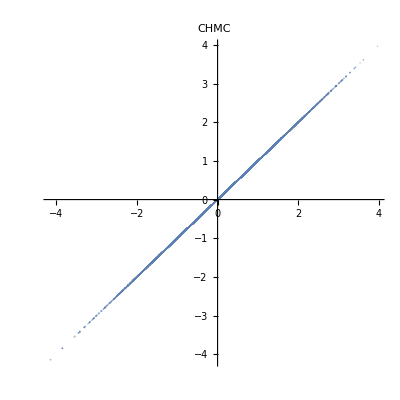

{0.990466,0.94797,0.995545,0.9384,0.984142,0.994789,0.950718,0.968886,0.970281,0.99487}

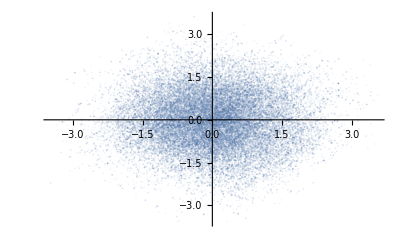

```mathematica
QS=hmc[U,dU,ddU,10,5000,10000,True,True];
ListPlot[QS[[;;,1;;2]],PlotLabel->CHMC,PlotStyle->Opacity[.2],AspectRatio->1]
QS1=QS.MatrixPower[SIGMA,-.5];
StandardDeviation[QS1]
ListPlot[QS1[[;;,1;;2]],PlotStyle->Opacity[.1]]
```

501 2.66846×10^8 60.9427 0.4 0.516398 2.60572×10^6 2.69452×10^8 1.7441×10^10 2.07965×10^-7 0.0001 True {1,2,4,7,11} {1,11}

1002 3826.17 65.3355 0.738191 0.355499 45.9048 3872.07 1.7441×10^10 2.07965×10^-7 0.0001 True {1,4,6,8,10,11} {1,11}

1503 3049.46 42.1984 0.417549 0.241711 43.82 3093.28 1.7441×10^10 2.07965×10^-7 0.0001 True {1,2} {11}

2004 3049.48 39.6957 0.439537 0.406499 43.7995 3093.28 1.7441×10^10 2.28762×10^-7 0.0001 True {1,2,4,7,11} {1,11}

2505 3076.95 44.8901 0.689193 0.278429 42.0109 3118.96 1.7441×10^10 1.71872×10^-7 0.0001 True {1,11} {1,11}

3006 3390.41 50.2328 0.577272 0.343582 42.8667 3433.27 1.7441×10^10 2.07965×10^-7 0.0001 True {1,4,8,11} {1,11}

3507 2688.95 54.7795 0.710051 0.291826 49.7787 2738.73 1.7441×10^10 2.07965×10^-7 0.0001 True {1,3,4,8,10,11} {1,11}

4008 3388.76 45.0411 0.702715 0.336719 43.1953 3431.95 1.7441×10^10 1.56247×10^-7 0.0001 True {1,9,10,11} {1,11}

4509 2955.92 53.173 0.614021 0.338783 44.5342 3000.46 1.7441×10^10 2.07965×10^-7 0.0001 True {1,7,10,11} {1,11}

5010 3776.18 38.9993 0.561639 0.287905 45.951 3822.13 1.7441×10^10 1.89059×10^-7 0.0001 True {1,2,3,4,5,9} {1,11}

5511 3766.25 36.326 0.562104 0.390224 55.8803 3822.13 1.7441×10^10 1.89059×10^-7 0.0001 True {1,6,11} {1,11}

6012 3781.84 36.4899 0.640592 0.303015 40.29 3822.13 1.7441×10^10 1.89059×10^-7 0.0001 True {1,2,4,11} {1,11}

6513 3770.84 52.5576 0.770427 0.298989 51.2875 3822.13 1.7441×10^10 1.89059×10^-7 0.0001 True {1,2,3,5,6,11} {1,11}

7014 3782.51 55.3105 0.562799 0.345735 39.6162 3822.13 1.7441×10^10 1.89059×10^-7 0.0001 True {1,2,6,11} {1,11}

7515 3779.64 41.8325 0.646905 0.379198 42.4856 3822.13 1.7441×10^10 1.89059×10^-7 0.0001 True {1,2,4,7,9,10,11} {1,11}

8016 3771.37 44.3257 0.619514 0.3542 50.7548 3822.13 1.7441×10^10 1.89059×10^-7 0.0001 True {1,4,5,11} {1,11}

8517 3778.35 54.1824 0.736611 0.361783 43.7794 3822.13 1.7441×10^10 1.89059×10^-7 0.0001 True {1,2,7,10,11} {1,11}

9018 3758.54 48.7479 0.626991 0.37035 63.5904 3822.13 1.7441×10^10 1.89059×10^-7 0.0001 True {1,3,4,5,7,11} {1,11}

9519 3783.85 58.3256 0.613655 0.316052 38.2787 3822.13 1.7441×10^10 1.89059×10^-7 0.0001 True {1,2,3,7,11} {1,11}

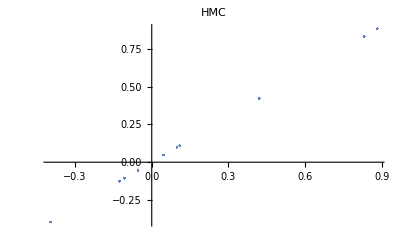

{0.976189,0.951869,0.925818,0.944036,0.949479,0.924375,0.944445,0.947855,0.949218,0.92769}

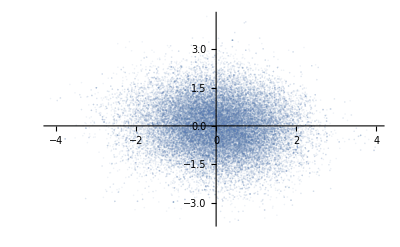

```mathematica
QS=hmc[U,dU,ddU,10,5000,10000,True,False];
ListPlot[QS[[;;,1;;2]],PlotLabel->HMC,PlotStyle->Opacity[.1]]
QS1=QS.MatrixPower[SIGMA,-.5];
StandardDeviation[QS1]
ListPlot[QS1[[;;,1;;2]],PlotStyle->Opacity[.1]]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{4.5×10^8,-5.×10^7,-5.×10^7,-5.×10^7,-5.×10^7,-5.×10^7,-5.×10^7,-5.×10^7,-5.×10^7,-5.×10^7},«8»,{-5.×10^7,-5.×10^7,«7»,4.5×10^8}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

501 2.0833×10^10 34.9089 0.3 0.483046 1.50955×10^9 2.07461×10^10 2.23426×10^10 1.×10^-9 0.012913 False {1,3,7,11} {1,11}

1002 4.89643×10^9 25.2033 0.1 0.316228 3.97521×10^8 2.07461×10^10 5.29395×10^9 1.×10^-9 0.00547637 False {1,2,3,11} {1,11}

1503 2.1549×10^9 45.8664 0.3 0.483046 3.00896×10^8 2.07461×10^10 2.4558×10^9 1.×10^-9 0.00374043 False {1,3,5,7,11} {1,11}

2004 1.57342×10^9 62.3775 0.3 0.483046 1.72763×10^8 2.07461×10^10 1.74619×10^9 1.×10^-9 0.00728905 False {1,2,4,5,10,11} {1,2,8,11}

2505 6.57692×10^8 58.0247 0.3 0.483046 8.67143×10^7 2.07461×10^10 7.44406×10^8 1.×10^-9 0.00662641 False {1,2,7,11} {1,11}

3006 2.20228×10^8 14.6965 0.3 0.483046 1.95026×10^7 2.07461×10^10 2.3973×10^8 1.×10^-9 0.00881975 False {1,9,11} {1,11}

3507 6.99363×10^7 56.2766 0.3 0.483046 7.6015×10^6 2.07461×10^10 7.75378×10^7 1.×10^-9 0.00602401 False {1,3,6,8,11} {1,11}

4008 3.1912×10^7 65.0908 0.4 0.516398 3.80334×10^6 2.07461×10^10 3.57153×10^7 1.×10^-9 0.00662641 False {1,3,7,11} {1,11}

4509 1.44623×10^7 57.3955 0.3 0.483046 2.20242×10^6 2.07461×10^10 1.66647×10^7 1.×10^-9 0.00452593 False {1,3,4,6,11} {1,11}

5010 9.70465×10^6 14.7082 0.4 0.516398 1.39472×10^6 2.07461×10^10 1.10994×10^7 1.×10^-9 0.00602401 False {1,2,11} {1,2,11}

5511 6.61924×10^6 59.9018 0.4 0.516398 593825. 2.07461×10^10 7.21307×10^6 1.×10^-9 0.00728905 False {1,2,3,11} {1,3,11}

6012 2.25139×10^6 51.7943 0.5 0.527046 355038. 2.07461×10^10 2.60643×10^6 1.×10^-9 0.00452593 False {1,2,3,11} {1,2,11}

6513 1.47754×10^6 65.8516 0.4 0.516398 250464. 2.07461×10^10 1.728×10^6 1.×10^-9 0.00452593 False {1,2,11} {1,11}

7014 871331. 77.3564 0.4 0.516398 89885.5 2.07461×10^10 961217. 1.×10^-9 0.00970172 False {1,4,11} {1,2,11}

7515 190475. 47.3262 0.300384 0.482782 25821.2 2.07461×10^10 216296. 1.×10^-9 0.00452593 False {1,2,11} {1,11}

8016 152829. 27.2245 0.408305 0.509877 14850.7 2.07461×10^10 167679. 1.×10^-9 0.00801795 False {1,2,8,11} {1,2,9,11}

8517 40710.2 84.9288 0.496854 0.503962 5221.41 2.07461×10^10 45931.6 1.×10^-9 0.00602401 False {1,2,6,11} {1,11}

9018 20899.8 35.1165 0.28805 0.383159 2041.22 2.07461×10^10 22941. 1.×10^-9 0.00547637 False {1,3,5,11} {1,11}

9519 15162.2 34.3814 0.364115 0.450539 956.15 2.07461×10^10 16118.3 1.×10^-9 0.00602401 False {1,2,8,10,11} {1,11}

10020 14229. 10.5985 0.442552 0.486101 509.984 2.07461×10^10 14739. 1.×10^-9 0.00547637 False {1,4,6,11} {1,11}

10521 13095.8 43.6764 0.666395 0.42311 346.951 2.07461×10^10 13442.7 1.×10^-9 0.00340039 False {1,4,5,9,11} {1,11}

11022 13190. 64.5693 0.442132 0.411937 252.699 2.07461×10^10 13442.7 1.×10^-9 0.00411448 False {1,3,4,5,9,11} {1,11}

11523 13269. 38.3998 0.477251 0.456991 173.714 2.07461×10^10 13442.7 1.×10^-9 0.00374043 False {1,2,11} {1,11}

12024 12200.2 58.8438 0.537762 0.358107 126.954 2.07461×10^10 12327.1 1.×10^-9 0.00281024 False {1,5,11} {1,11}

12525 8984.89 73.149 0.722724 0.373617 91.636 2.07461×10^10 9076.53 1.×10^-9 0.00340039 False {1,5,6,7,11} {1,11}

13026 5279.79 103.285 0.533951 0.442772 61.0754 2.07461×10^10 5340.86 1.×10^-9 0.00547637 False {1,3,6,7,9,11} {1,11}

13527 1379.06 50.8015 0.545147 0.47818 17.9474 2.07461×10^10 1397.01 1.×10^-9 0.012913 False {1,4,9,11} {1,11}

14028 99.1451 24.0004 0.559436 0.382728 5.49693 2.07461×10^10 104.642 1.×10^-9 0.0251638 False {1,2,5,11} {1,11}

14529 66.4038 34.4212 0.449237 0.406692 5.38473 2.07461×10^10 71.7885 1.×10^-9 0.0445792 False {1,2,5,11} {1,11}

15030 68.3816 49.3546 0.68745 0.407939 3.40695 2.07461×10^10 71.7885 1.×10^-9 0.0368423 False {1,2,5,7,11} {1,11}

15531 68.5553 54.7014 0.464589 0.356901 3.23325 2.07461×10^10 71.7885 1.×10^-9 0.0368423 False {1,4,6} {1,11}

16032 64.5472 53.8277 0.727903 0.354944 7.24135 2.07461×10^10 71.7885 1.×10^-9 0.0368423 False {1,2,3,8,11} {1,10,11}

16533 67.5011 39.2459 0.710332 0.347851 4.2874 2.07461×10^10 71.7885 1.×10^-9 0.0368423 False {1,2,4,7,10,11} {1,11}

17034 67.9073 43.2088 0.523891 0.414827 3.88125 2.07461×10^10 71.7885 1.×10^-9 0.0368423 False {1,4,7,9} {1,11}

17535 64.2978 33.8431 0.667948 0.417975 7.49069 2.07461×10^10 71.7885 1.×10^-9 0.0368423 False {1,5,8,9,10,11} {1,11}

18036 65.6446 43.1837 0.725257 0.409638 6.14391 2.07461×10^10 71.7885 1.×10^-9 0.0368423 False {1,2,11} {1,6,11}

18537 68.2786 48.1936 0.596681 0.421195 3.50993 2.07461×10^10 71.7885 1.×10^-9 0.0368423 False {1,7,10,11} {1,11}

19038 68.7893 76.0168 0.624859 0.312079 2.99918 2.07461×10^10 71.7885 1.×10^-9 0.0368423 False {1,3,5,6,10} {1,11}

19539 68.4629 50.1733 0.66577 0.369779 3.32559 2.07461×10^10 71.7885 1.×10^-9 0.0368423 False {1,4,5,10,11} {1,11}

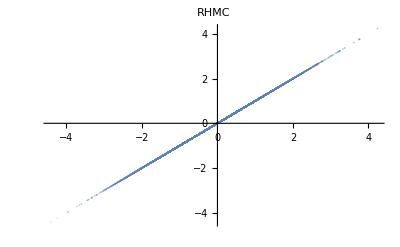

{0.306959,0.306959,0.306959,0.306959,0.306959,0.306959,0.306959,0.306959,0.306959,0.306959}

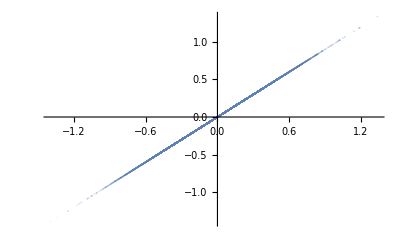

```mathematica
QS=hmc[U,dU,ddU,10,15000,20000,False,False];
ListPlot[QS[[;;,1;;2]],PlotLabel->RHMC,PlotStyle->Opacity[.2]]
QS1=QS.MatrixPower[SIGMA,-.5];
StandardDeviation[QS1]
ListPlot[QS1[[;;,1;;2]],PlotStyle->Opacity[.1]]
```